# The CPOP Algorithm

— Clayton Shonkwiler and Kandin Theis, 2025

This notebook gives reference implementations of the algorithms from our paper “Direct Sampling of Confined Polygons in Linear Time” as compiled Mathematica function.

## Confined Polytope Sample

This is Algorithm 1 from the paper. It is heavily inspired by work of Marchal.

```mathematica
ConfinedPolytopeSample=Compile[{{n,_Integer}},
Module[{u,d,α,t},
Label[begin];
u=RandomReal[{0,1},n];
d=Prepend[Table[0.,{n-1}],u[[1]]];
Table[d[[k+1]]=1-2/π ArcSin[u[[k+1]]Sin[π/2 d[[k]]]],{k,1,n-1}];
α=Sin[π/2 d[[n]]]/Sin[π/2 d[[1]]];
t=RandomReal[];
If[t<2/(α+1/α),If[t<1/(α+1/α),d=Reverse[d]],Goto[begin]];
d
]
]
```

CompiledFunction[…]

## CPOP

This is Algorithm 2 from the paper. The polygon reconstruction algorithm (which is essentially all of the following code) is essentially transcribed from the fan_triangulation_action function in plCurve.

```mathematica
CPOP=Compile[{{n,_Integer}},
Block[{d,p,c,e,v,nu,cosalpha,sinalpha,factor,θ,cosθ,sinθ,factor2},
d=Join[{1.},ConfinedPolytopeSample[n-3],{1.}]  (* Generate diagonals using ConfinedPolytopeSample *) ;
p=Table[{0.,0.,0.},n] (* Initialize vertex positions *) ; 
p[[2]]={1.,0.,0.};
c=p[[2]];
e={1.,0.,0.} (* Current edge vector *); 
nu={0.,0.,1.} (* Triangle normal *);
(* Now we reconstruct the polygon *)
Table[ 
cosalpha=(d[[i]]^2+d[[i+1]]^2-1.)/(2.*d[[i]]*d[[i+1]]);
sinalpha=√(1-cosalpha^2);
v=Cross[nu,e];
factor=Dot[nu,e]*(1.-cosalpha);
e=Normalize[cosalpha*e+sinalpha*v+factor*nu];
p[[i+2]]=d[[i+1]]*e;
c+=p[[i+2]];
v=Cross[e,nu];
θ=RandomReal[{-π,π}] (* The dihedrals are all uniform on [-π,π) *); 
cosθ=Cos[θ];
sinθ=Sin[θ];
factor2=Dot[e,nu]*(1.-cosθ);
nu=Normalize[cosθ*nu+sinθ*v+factor2*e];,
{i,1,n-3}
];
cosalpha=(d[[n-2]]^2+d[[n-1]]^2-1.)/(2.*d[[n-2]]*d[[n-1]]);
sinalpha=√(1-cosalpha^2);
v=Cross[nu,e];
factor=Dot[nu,e]*(1.-cosalpha);
e=Normalize[cosalpha*e+sinalpha*v+factor*nu];
p[[n]]=d[[n-1]]*e;
p
]]
```

CompiledFunction[…]

## Example Usage

We can generate 1000 random confined 500-gons with:

```mathematica
confined500gons=ParallelTable[CPOP[500],{1000}];
```

And compare the histogram of distances   to the asymptotic density :

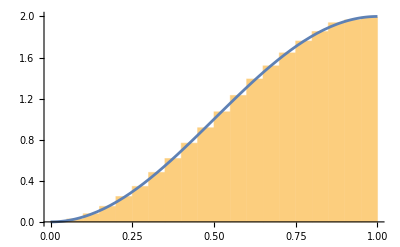

```mathematica
Show[Histogram[Norm/@Flatten[confined500gons[[;;,3;;499]],1],Automatic,"PDF"],Plot[1-Cos[π t],{t,0,1}]]
```

(Note, we exclude , which always has distance 0, and  and , which always have distance 1.)